{{140.377,27.7094,3.03571×10^13},{181.172,15.684,1.59111×10^13},{24.3811,25.6877,2.7874×10^13},{49.2375,17.7028,2.03612×10^13},19972,{39.7853,26.016,2.88062×10^13},{348.64,17.4986,1.75931×10^13},{263.657,26.7356,2.46945×10^13},{231.519,24.5662,2.29935×10^13}}
 |  |  |  |

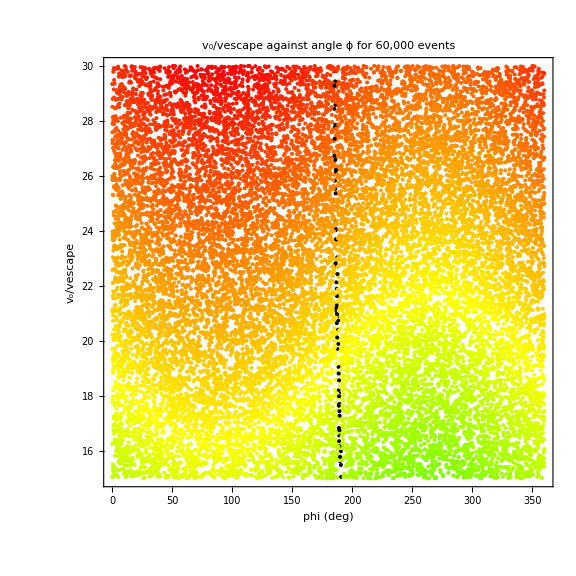

```mathematica
(* Lab 13 Plotting *) 

t1 = ReadList["C:\\Users\\Omair\\Documents\\Spring Semester 2015\\Computational Methods\\Lab12\\total3.dat",{Number,Number,Number}]
myNmax=Length[t1];
mymin=1*10^75;
i=1;
While[i<myNmax,
If[ t1[[i,3]]<mymin,If[t1[[i,3]]>0,mymin=t1[[i,3]]]];
i=i+1]
mymax=Max[Table[t1[[i,3]],{i,1,myNmax}]];
range=mymax-mymin;
(* Make the final table with the color code for the final distance as the last element. *)
t2=Table[
{t1[[i,1]],
t1[[i,2]],
If[t1[[i,3]]<0,If[t1[[i,3]]==-1,0.9,0.7],0.25*(1-((t1[[i,3]]-mymin)/range))]},{i,1,myNmax}
];
(*Define the plotting function.Underscore means hold value until defined*)ThreeBodyScatterPlot[data_/;MatrixQ[data,NumberQ]&&(*Matrix Q elvaluates true if data is an array AND has 3 numbers in a data set*)Length[First[data]]===3,fun_,opts___]:=Show[Graphics[{PointSize[0.005],Map[{fun[Last[#]],Point[Take[#,2]]}&,data]},opts]]

(*Make the plot.*)p5=ThreeBodyScatterPlot[t2,Hue[#,1,If[#==0.9,0,1]]&,(*applies color according to hitting the sun,earth or inbetween*)Axes->True,AxesLabel->{"x","y","z"},PlotLabel -> ("  v_0/vescape against angle ϕ for 60,000 events"),AspectRatio->1,Frame->True,LabelStyle->{FontSize->14, Directive[Bold,Black]},PlotRange->{{0,360},{15,30}},BaseStyle->FontSize->16,ImageSize->8*72,Frame->True,FrameLabel->{"phi (deg)","v_o/vescape"}]
```